```mathematica
(*The dispersion relation*)
$Assumptions->{v>0,0<u<1};
a=ϵ;
b=(g^2-ϵ^2+2 ϵ Subscript[n, z]^2-ϵ Subscript[ϵ, l]+Subscript[n, y]^2 (ϵ+Subscript[ϵ, l]));
c=ϵ Subscript[n, z]^4+(Subscript[n, y]^4-2 ϵ Subscript[n, y]^2-g^2+ϵ^2) Subscript[ϵ, l]+Subscript[n, z]^2 (g^2+(Subscript[n, y]^2 -ϵ)(ϵ+Subscript[ϵ, l]));
disp={{Ν->((ϵ-Subscript[n, y]^2 )(ϵ+Subscript[ϵ, l])-g^2+√(Subscript[n, y]^4 (ϵ-Subscript[ϵ, l])^2+(g^2-ϵ^2+ϵ Subscript[ϵ, l])^2+2 Subscript[n, y]^2 (g^2(ϵ+Subscript[ϵ, l])-ϵ(ϵ-Subscript[ϵ, l])^2)))/(2 ϵ)-Subscript[n, z]^2},{Ν->((ϵ-Subscript[n, y]^2 )(ϵ+Subscript[ϵ, l])-g^2-√(Subscript[n, y]^4 (ϵ-Subscript[ϵ, l])^2+(g^2-ϵ^2+ϵ Subscript[ϵ, l])^2+2 Subscript[n, y]^2 (g^2(ϵ+Subscript[ϵ, l])-ϵ(ϵ-Subscript[ϵ, l])^2)))/(2 ϵ)-Subscript[n, z]^2}};(*Ν=Subscript[n, x]^2*)
Ο=(Ν/.disp⟦1⟧)/.{ϵ->1-v/(1-u),Subscript[ϵ, l]->1-v,g->(v √u)/(1-u),Subscript[n, y]->Cos[θ]Sin[η],Subscript[n, z]->Sin[θ]}//Simplify;
X=(Ν/.disp⟦2⟧)/.{ϵ->1-v/(1-u),Subscript[ϵ, l]->1-v,g->(v √u)/(1-u),Subscript[n, y]->Cos[θ]Sin[η],Subscript[n, z]->Sin[θ]}//Simplify;
Subscript[e, y]/Subscript[e, z]==(Csc[η] Sec[θ] (1-Cos[θ]^2 Sin[η]^2) (√u(1- Cos[θ]^2 Sin[η]^2)±√(u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4)))/(2 ⅈ  Cos[η] Cos[θ]-(√u(1- Cos[θ]^2 Sin[η]^2)±√(u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4)) Sin[θ]);(*plasma polarisations as v->0; "+" for "O" and "-" for "X"*)
Clear[a,b,c,disp]
```

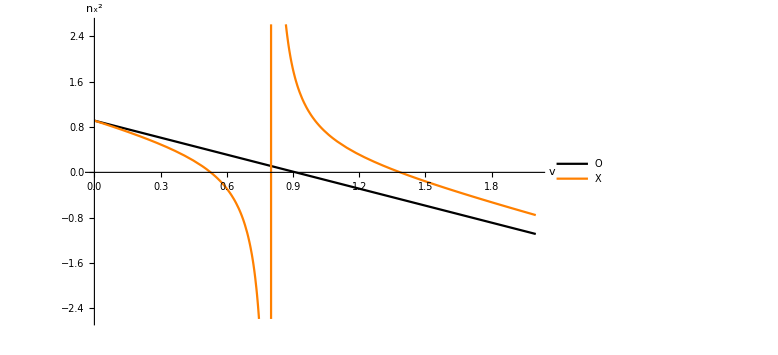

```mathematica
(*η=0*)
params={u->0.2,θ->0.3,η->0};
Plot[{Ο/.params,X/.params},{v,0,2},PlotStyle->{Black,Orange},PlotRange->{All,Automatic},PlotLegends->Placed[{"Ο","X"},Scaled[{0.7,0.7}]],ImageSize->Large,AxesLabel->{v,Subscript[n, x]^2},LabelStyle->{FontSize->20}]
(*SaveData["results/dispersionRelations/eta.png",%,"PNG"]*)
Clear[params];
```

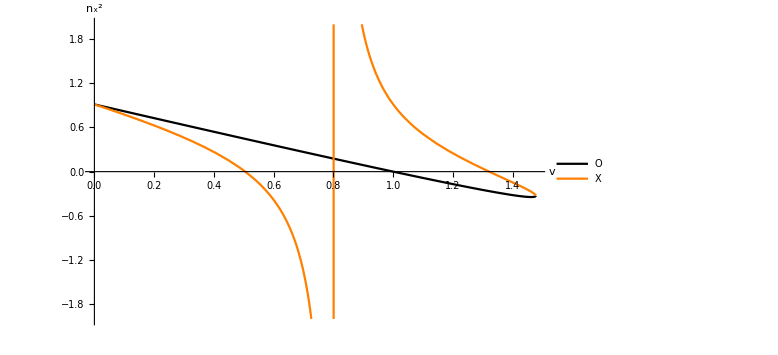

```mathematica
(*θ=0*)
params={u->0.2,θ->0,η->0.3};
Plot[{Ο/.params,X/.params},{v,0,2},PlotStyle->{Black,Orange},PlotRange->{All,{-2,2}},PlotLegends->Placed[{"Ο","X"},Scaled[{0.9,0.8}]],ImageSize->Large,AxesLabel->{v,Subscript[n, x]^2},LabelStyle->{FontSize->20}]
(*SaveData["results/dispersionRelations/teta.png",%,"PNG"]*)
Clear[params];
```

```mathematica
$Assumptions={-π/2<θ<π/2,-π/2<η<π/2};
sol=Solve[{Subscript[e, y] Subscript[n, x] Subscript[n, y]+Subscript[e, z] (ⅈ g+Subscript[n, x] Subscript[n, z])+Subscript[e, x] (ϵ-Subscript[n, y]^2-Subscript[n, z]^2)==0,Subscript[e, z] (ϵ-Subscript[n, x]^2-Subscript[n, y]^2)+Subscript[e, y] Subscript[n, y] Subscript[n, z]+Subscript[e, x] (-ⅈ g+Subscript[n, x] Subscript[n, z])==0},{Subscript[e, y],Subscript[e, z]}]⟦1⟧/.Solve[Subscript[e, x] Subscript[n, x] Subscript[n, y]+Subscript[e, z] Subscript[n, y] Subscript[n, z]+Subscript[e, y] (-Subscript[n, x]^2-Subscript[n, z]^2+Subscript[ϵ, l])==0,Subscript[e, x]]⟦1⟧;
Subscript[Π, o]=Subscript[e, y]/Subscript[e, z]/.sol/.Subscript[n, x]->√Ο/.{ϵ->1-v/(1-u),Subscript[ϵ, l]->1-v,g->(v √u)/(1-u),Subscript[n, y]->Cos[θ]Sin[η],Subscript[n, z]->Sin[θ]};
Subscript[P, o]=Limit[Subscript[Π, o],v->0]//Simplify
Subscript[Π, x]=Subscript[e, y]/Subscript[e, z]/.sol/.Subscript[n, x]->√X/.{ϵ->1-v/(1-u),Subscript[ϵ, l]->1-v,g->(v √u)/(1-u),Subscript[n, y]->Cos[θ]Sin[η],Subscript[n, z]->Sin[θ]};
Subscript[P, x]=Limit[Subscript[Π, x],v->0]//Simplify
```

```mathematica
$Assumptions={-π/2<$θ<π/2,-π/2<$η<π/2}
Subscript[e, y^o]=(6+2 Cos[2 η]+Cos[2 η-2 θ]-2 Cos[2 θ]+Cos[2 (η+θ)]) Csc[η]^3 Sec[θ]^3 (6 u+2 u Cos[2 η]+u Cos[2 η-2 θ]-2 u Cos[2 θ]+u Cos[2 (η+θ)]+8 √(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4)));
Subscript[e, z^o]=64 (2 ⅈ √u Cot[η] Csc[η] Sec[θ]+u Sin[θ]+Csc[η]^2 Sec[θ] (-√(u (u Cos[θ]^4-2 (-2+u) Cos[θ]^2 Csc[η]^2+u Csc[η]^4) Sin[η]^4)-u ) Tan[θ]);
Subscript[e, y^x]=(6+2 Cos[2 η]+Cos[2 η-2 θ]-2 Cos[2 θ]+Cos[2 (η+θ)]) Csc[η]^3 Sec[θ]^3 (6 u+2 u Cos[2 η]+u Cos[2 η-2 θ]-2 u Cos[2 θ]+u Cos[2 (η+θ)]-8 √(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4)));
Subscript[e, z^x]=64 (2 ⅈ √u Cot[η] Csc[η] Sec[θ]+u Sin[θ]+Csc[η]^2 Sec[θ] (√(u (u Cos[θ]^4-2 (-2+u) Cos[θ]^2 Csc[η]^2+u Csc[η]^4) Sin[η]^4)-u ) Tan[θ]);
Inverse[Subscript[Υ, vacuum]].({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, Sin[$θ]Tan[$η], (Sin[$θ]^2-Cos[$θ]^2 Cos[$η]^2)/(Cos[$θ]Cos[$η])}, {0, 0, (Cos[$θ]Cos[2$η])/Cos[$η], -Sin[$θ]Tan[$η]}}).({{Subscript[e, y^o], Subscript[e, y^x], Subscript[e, y^o], Subscript[e, y^x]}, {Subscript[e, z^o], Subscript[e, z^x], Subscript[e, z^o], Subscript[e, z^x]}, {Subscript[e, y^o], Subscript[e, y^x], -Subscript[e, y^o], -Subscript[e, y^x]}, {Subscript[e, z^o], Subscript[e, z^x], -Subscript[e, z^o], -Subscript[e, z^x]}})/.{θ->$θ,η->$η,u->$u}//Simplify
```

{-π/2<$θ<π/2,-π/2<$η<π/2}

{{(6+2 Cos[2 $η]+Cos[2 $η-2 $θ]-2 Cos[2 $θ]+Cos[2 ($η+$θ)]) Cot[$η] Csc[$η]^2 Sec[$θ]^3 (6 $u+2 $u Cos[2 $η]+$u Cos[2 $η-2 $θ]-2 $u Cos[2 $θ]+$u Cos[2 ($η+$θ)]+8 √($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4))),(6+2 Cos[2 $η]+Cos[2 $η-2 $θ]-2 Cos[2 $θ]+Cos[2 ($η+$θ)]) Cot[$η] Csc[$η]^2 Sec[$θ]^3 (6 $u+2 $u Cos[2 $η]+$u Cos[2 $η-2 $θ]-2 $u Cos[2 $θ]+$u Cos[2 ($η+$θ)]-8 √($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4))),4 Csc[$η] Sec[$θ] (4 $u Cos[$η]^3 Cos[$θ]^2+1/2 Cos[$η] (22 $u+6 $u Cos[2 $η]+3 $u Cos[2 $η-2 $θ]-10 $u Cos[2 $θ]+3 $u Cos[2 ($η+$θ)]+32 √($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4)))+32 ⅈ √($u) Tan[$θ]),-4 Csc[$η] Sec[$θ] (-4 $u Cos[$η]^3 Cos[$θ]^2-1/2 Cos[$η] (22 $u+6 $u Cos[2 $η]+3 $u Cos[2 $η-2 $θ]-10 $u Cos[2 $θ]+3 $u Cos[2 ($η+$θ)]-32 √($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4)))-32 ⅈ √($u) Tan[$θ])},{-(6+2 Cos[2 $η]+Cos[2 $η-2 $θ]-2 Cos[2 $θ]+Cos[2 ($η+$θ)]) Csc[$η]^2 Sec[$θ]^2 (6 $u+2 $u Cos[2 $η]+$u Cos[2 $η-2 $θ]-2 $u Cos[2 $θ]+$u Cos[2 ($η+$θ)]+8 √($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4))) Tan[$θ]+32 Sec[$θ] (2 ⅈ √($u) Cot[$η] Csc[$η] Sec[$θ]+$u Sin[$θ]-Csc[$η]^2 Sec[$θ] ($u+√($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4))) Tan[$θ])-32 Cot[$η] (-1+Tan[$θ]^2) ($u Cos[$θ] Sin[$θ] Tan[$η]-Csc[$η] (-2 ⅈ √($u)+Sec[$η] ($u+√($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4))) Tan[$θ])),-(6+2 Cos[2 $η]+Cos[2 $η-2 $θ]-2 Cos[2 $θ]+Cos[2 ($η+$θ)]) Csc[$η]^2 Sec[$θ]^2 (6 $u+2 $u Cos[2 $η]+$u Cos[2 $η-2 $θ]-2 $u Cos[2 $θ]+$u Cos[2 ($η+$θ)]-8 √($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4))) Tan[$θ]+32 Sec[$θ] (2 ⅈ √($u) Cot[$η] Csc[$η] Sec[$θ]+$u Sin[$θ]+Csc[$η]^2 Sec[$θ] (-$u+√($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4))) Tan[$θ])-32 (2 ⅈ √($u) Cot[$η] Csc[$η]+$u Cos[$θ] Sin[$θ]-$u Csc[$η]^2 Tan[$θ]+Csc[$η]^2 √($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4)) Tan[$θ]) (-1+Tan[$θ]^2),4 Csc[$η] (2 $u Cos[$η]^3 Cot[$η] Sin[2 $θ]-6 $u Cos[$η]^2 Sin[$η] Sin[2 $θ]+2 Cos[$η] Cot[$η] (7 $u-$u Cos[2 $θ]+8 √($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4))) Tan[$θ]+32 ⅈ √($u) Cot[$η] Tan[$θ]^2),4 Csc[$η] (2 $u Cos[$η]^3 Cot[$η] Sin[2 $θ]-6 $u Cos[$η]^2 Sin[$η] Sin[2 $θ]-2 Cos[$η] Cot[$η] (-7 $u+$u Cos[2 $θ]+8 √($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4))) Tan[$θ]+32 ⅈ √($u) Cot[$η] Tan[$θ]^2)},{-4 Csc[$η] Sec[$θ] (4 $u Cos[$η]^3 Cos[$θ]^2+1/2 Cos[$η] (22 $u+6 $u Cos[2 $η]+3 $u Cos[2 $η-2 $θ]-10 $u Cos[2 $θ]+3 $u Cos[2 ($η+$θ)]+32 √($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4)))+32 ⅈ √($u) Tan[$θ]),4 Csc[$η] Sec[$θ] (-4 $u Cos[$η]^3 Cos[$θ]^2-1/2 Cos[$η] (22 $u+6 $u Cos[2 $η]+3 $u Cos[2 $η-2 $θ]-10 $u Cos[2 $θ]+3 $u Cos[2 ($η+$θ)]-32 √($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4)))-32 ⅈ √($u) Tan[$θ]),-(6+2 Cos[2 $η]+Cos[2 $η-2 $θ]-2 Cos[2 $θ]+Cos[2 ($η+$θ)]) Cot[$η] Csc[$η]^2 Sec[$θ]^3 (6 $u+2 $u Cos[2 $η]+$u Cos[2 $η-2 $θ]-2 $u Cos[2 $θ]+$u Cos[2 ($η+$θ)]+8 √($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4))),-(6+2 Cos[2 $η]+Cos[2 $η-2 $θ]-2 Cos[2 $θ]+Cos[2 ($η+$θ)]) Cot[$η] Csc[$η]^2 Sec[$θ]^3 (6 $u+2 $u Cos[2 $η]+$u Cos[2 $η-2 $θ]-2 $u Cos[2 $θ]+$u Cos[2 ($η+$θ)]-8 √($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4)))},{-2 Cot[$η] Csc[$η] Sec[$θ] (8 $u Cos[$η]^3 Cos[$θ]^3+Cos[$η] Cos[$θ] (22 $u+6 $u Cos[2 $η]+3 $u Cos[2 $η-2 $θ]-10 $u Cos[2 $θ]+3 $u Cos[2 ($η+$θ)]+32 √($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4)))+64 ⅈ √($u) Sin[$θ]) Tan[$θ],-4 Csc[$η] (2 $u Cos[$η]^3 Cot[$η] Sin[2 $θ]-6 $u Cos[$η]^2 Sin[$η] Sin[2 $θ]-2 Cos[$η] Cot[$η] (-7 $u+$u Cos[2 $θ]+8 √($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4))) Tan[$θ]+32 ⅈ √($u) Cot[$η] Tan[$θ]^2),(6+2 Cos[2 $η]+Cos[2 $η-2 $θ]-2 Cos[2 $θ]+Cos[2 ($η+$θ)]) Csc[$η]^2 Sec[$θ]^2 (6 $u+2 $u Cos[2 $η]+$u Cos[2 $η-2 $θ]-2 $u Cos[2 $θ]+$u Cos[2 ($η+$θ)]+8 √($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4))) Tan[$θ]-32 Sec[$θ] (2 ⅈ √($u) Cot[$η] Csc[$η] Sec[$θ]+$u Sin[$θ]-Csc[$η]^2 Sec[$θ] ($u+√($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4))) Tan[$θ])+32 Cot[$η] (-1+Tan[$θ]^2) ($u Cos[$θ] Sin[$θ] Tan[$η]-Csc[$η] (-2 ⅈ √($u)+Sec[$η] ($u+√($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4))) Tan[$θ])),(6+2 Cos[2 $η]+Cos[2 $η-2 $θ]-2 Cos[2 $θ]+Cos[2 ($η+$θ)]) Csc[$η]^2 Sec[$θ]^2 (6 $u+2 $u Cos[2 $η]+$u Cos[2 $η-2 $θ]-2 $u Cos[2 $θ]+$u Cos[2 ($η+$θ)]-8 √($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4))) Tan[$θ]-32 Sec[$θ] (2 ⅈ √($u) Cot[$η] Csc[$η] Sec[$θ]+$u Sin[$θ]+Csc[$η]^2 Sec[$θ] (-$u+√($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4))) Tan[$θ])+32 (2 ⅈ √($u) Cot[$η] Csc[$η]+$u Cos[$θ] Sin[$θ]-$u Csc[$η]^2 Tan[$θ]+Csc[$η]^2 √($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4)) Tan[$θ]) (-1+Tan[$θ]^2)}}

```mathematica
MatrixForm[%154]/.{$θ->π/4,$η->π/3,$u->1/2}//N
```

(107.402 | -52.9684 | 64.4409+147.802 ⅈ | -31.7811+147.802 ⅈ
-236.771+60.3398 ⅈ | 116.771+60.3398 ⅈ | 26.3079+60.3398 ⅈ | -12.9746+60.3398 ⅈ
-64.4409-147.802 ⅈ | 31.7811-147.802 ⅈ | -107.402 | 52.9684
-26.3079-60.3398 ⅈ | 12.9746-60.3398 ⅈ | 236.771-60.3398 ⅈ | -116.771-60.3398 ⅈ)

```mathematica
Subscript[P, x]/.{θ->0};
Limit[%,η->0]/.u->0.5//Simplify
```

ComplexInfinity

```mathematica
disp={n->1-(2v(1-v))/(2(1-v)-u (1-Cos[θ]^2 Sin[η]^2)+√(u^2(1-Cos[θ]^2 Sin[η]^2)^2+4u(1-v)^2(Cos[θ]Sin[η])^2)),n->1-(2v(1-v))/(2(1-v)-u (1-Cos[θ]^2 Sin[η]^2)-√(u^2(1-Cos[θ]^2 Sin[η]^2)^2+4u(1-v)^2(Cos[θ]Sin[η])^2))};
Subscript[e, y^o]=n^2(1-Cos[θ]^2 Sin[η]^2)+v-1/.disp⟦1⟧;
Subscript[e, z^o]=n^2 Cos[θ]Sin[η](Sin[θ]+ⅈ(v √u Sin[η])/((1-u)n^2+v+u-1))/.disp⟦1⟧;
Subscript[e, y^x]=n^2(1-Cos[θ]^2 Sin[η]^2)+v-1/.disp⟦2⟧;
Subscript[e, z^x]=n^2 Cos[θ]Sin[η](Sin[θ]+ⅈ(v √u Sin[η])/((1-u)n^2+v+u-1))/.disp⟦2⟧;
Inverse[Subscript[Υ, vacuum]].({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -Sin[$θ]Tan[$η], -(Sin[$θ]^2+Cos[$θ]^2 Cos[$η]^2)/(Cos[$θ]Cos[$η])}, {0, 0, Cos[$θ]/Cos[$η], Sin[$θ]Tan[$η]}}).({{Subscript[e, y^o], Subscript[e, y^x], -Subscript[e, y^o], -Subscript[e, y^x]}, {Subscript[e, z^o], Subscript[e, z^x], -Subscript[e, z^o], -Subscript[e, z^x]}, {Subscript[e, y^o], Subscript[e, y^x], Subscript[e, y^o], Subscript[e, y^x]}, {Subscript[e, z^o], Subscript[e, z^x], Subscript[e, z^o], Subscript[e, z^x]}})/.{θ->$θ,η->$η};
Limit[%,v->0]//Simplify//MatrixForm
```

(Sin[$η] (-Cos[$θ]^2+(ⅈ √u Sin[$η] (2-u+u Cos[$θ]^2 Sin[$η]^2+√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4))) Sin[$θ])/(-2+3 u+u Cos[$θ]^2 Sin[$η]^2+√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4)))+Sin[$θ]^2) Tan[$η] | Sin[$η] (-Cos[$θ]^2+(ⅈ √u Sin[$η] (2-u+u Cos[$θ]^2 Sin[$η]^2-√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4))) Sin[$θ])/(-2+3 u+u Cos[$θ]^2 Sin[$η]^2-√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4)))+Sin[$θ]^2) Tan[$η] | 0 | 0
1/2 ((2 ⅈ √u Sin[$η]^2 (2-u+u Cos[$θ]^2 Sin[$η]^2+√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4))))/(-2+3 u+u Cos[$θ]^2 Sin[$η]^2+√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4)))+Sin[$η] Sin[$θ]+Cos[$θ]^2 Sin[$η] Sin[$θ]+Sec[$η] Sin[$θ]^3 Tan[$η]-Sin[$η] Sin[$θ]^3 Tan[$η]^2) | 1/2 ((2 ⅈ √u Sin[$η]^2 (2-u+u Cos[$θ]^2 Sin[$η]^2-√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4))))/(-2+3 u+u Cos[$θ]^2 Sin[$η]^2-√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4)))+Sin[$η] Sin[$θ]+Cos[$θ]^2 Sin[$η] Sin[$θ]+Sec[$η] Sin[$θ]^3 Tan[$η]-Sin[$η] Sin[$θ]^3 Tan[$η]^2) | 0 | 0
0 | 0 | Sin[$η] (-Cos[$θ]^2+(ⅈ √u Sin[$η] (2-u+u Cos[$θ]^2 Sin[$η]^2+√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4))) Sin[$θ])/(-2+3 u+u Cos[$θ]^2 Sin[$η]^2+√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4)))+Sin[$θ]^2) Tan[$η] | Sin[$η] (-Cos[$θ]^2+(ⅈ √u Sin[$η] (2-u+u Cos[$θ]^2 Sin[$η]^2-√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4))) Sin[$θ])/(-2+3 u+u Cos[$θ]^2 Sin[$η]^2-√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4)))+Sin[$θ]^2) Tan[$η]
0 | 0 | 1/2 ((2 ⅈ √u Sin[$η]^2 (2-u+u Cos[$θ]^2 Sin[$η]^2+√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4))))/(-2+3 u+u Cos[$θ]^2 Sin[$η]^2+√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4)))+Sin[$η] Sin[$θ]+Cos[$θ]^2 Sin[$η] Sin[$θ]+Sec[$η] Sin[$θ]^3 Tan[$η]-Sin[$η] Sin[$θ]^3 Tan[$η]^2) | 1/2 ((2 ⅈ √u Sin[$η]^2 (2-u+u Cos[$θ]^2 Sin[$η]^2-√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4))))/(-2+3 u+u Cos[$θ]^2 Sin[$η]^2-√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4)))+Sin[$η] Sin[$θ]+Cos[$θ]^2 Sin[$η] Sin[$θ]+Sec[$η] Sin[$θ]^3 Tan[$η]-Sin[$η] Sin[$θ]^3 Tan[$η]^2))

```mathematica
MatrixForm[%291]/.{$θ->0.1,$η->0.000001,u->0}//N
```

(-9.80067×10^-13 | -9.80067×10^-13 | 0. | 0.
9.98334×10^-8 | 9.98334×10^-8 | 0. | 0.
0. | 0. | -9.80067×10^-13 | -9.80067×10^-13
0. | 0. | 9.98334×10^-8 | 9.98334×10^-8)

```mathematica
n^2 Cos[θ]Sin[η](Sin[θ]+ⅈ(g Sin[η])/(n^2-ϵ))/.disp⟦1⟧/.{ϵ->1-v/(1-u),Subscript[ϵ, l]->1-v,g->(v √u)/(1-u)};
Limit[%,v->0]//Simplify
```

Cos[θ] Sin[η] ((ⅈ √u Sin[η])/((1-u) (1/(1-u)-4/(2-u+u Cos[θ]^2 Sin[η]^2+√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4)))))+Sin[θ])

```mathematica
n^2 Cos[θ]Sin[η](Sin[θ]+ⅈ(g Sin[η])/(n^2-ϵ))/.disp⟦2⟧/.{ϵ->1-v/(1-u),Subscript[ϵ, l]->1-v,g->(v √u)/(1-u)};
Limit[%,v->0]//Simplify
```

Cos[θ] Sin[η] ((ⅈ √u Sin[η])/((1-u) (1/(1-u)+4/(-2+u-u Cos[θ]^2 Sin[η]^2+√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4)))))+Sin[θ])

```mathematica
Limit[%298,$η->0]
```

$Aborted

```mathematica
(%291⟦{1,2},{1,2}⟧)/Det[%291⟦{1,2},{1,2}⟧]//Simplify
```

{{(Csc[$η]^2 Sec[$θ] (-2+3 u+u Cos[$θ]^2 Sin[$η]^2-√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4)))^3 (-2+3 u+u Cos[$θ]^2 Sin[$η]^2+√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4)))^2 (ⅈ u Cos[$θ]^3 Sin[$η]^2+Cos[$θ] (ⅈ (-2+3 u+√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4)))+u^(3/2) Sin[$η]^3 Sin[$θ]-ⅈ u Sin[$η]^2 Sin[$θ]^2)+(-√u Sin[$η] (-2+u-√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4)))-ⅈ (-2+3 u+√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4))) Sin[$θ]) Tan[$θ]))/(8 (-1+u)^3 √u (4-10 u+2 u Cos[2 $η]+u Cos[2 $η-2 $θ]-2 u Cos[2 $θ]+u Cos[2 ($η+$θ)])^2 √(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4))),-((Csc[$η]^2 Sec[$θ]^2 (2-3 u-u Cos[$θ]^2 Sin[$η]^2+√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4)))^2 (-2+3 u+u Cos[$θ]^2 Sin[$η]^2+√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4)))^3 (-ⅈ u Cos[$θ]^4 Sin[$η]^2+Sin[$θ] (√u Sin[$η] (-2+u+√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4)))-ⅈ (2-3 u+√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4))) Sin[$θ])+ⅈ Cos[$θ]^2 (2-3 u+√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4))+ⅈ u^(3/2) Sin[$η]^3 Sin[$θ]+u Sin[$η]^2 Sin[$θ]^2)))/(8 (-1+u)^3 √u (4-10 u+2 u Cos[2 $η]+u Cos[2 $η-2 $θ]-2 u Cos[2 $θ]+u Cos[2 ($η+$θ)])^2 √(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4))))},{(Cot[$η] Csc[$η]^2 Sec[$θ]^2 (16-26 u+2 u Cos[2 $η]+u Cos[2 $η-2 $θ]-2 u Cos[2 $θ]+u Cos[2 ($η+$θ)]-8 √(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4)))^2 (4 u Cos[2 $η]+2 (16-26 u+u Cos[2 $η-2 $θ]-2 u Cos[2 $θ]+u Cos[2 ($η+$θ)]+8 √(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4))))^3 (2 √u Sin[$η] (5 u-8 (2+√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4))))+2 u^(3/2) Sin[3 $η]+ⅈ u Sin[2 $η-3 $θ]-3 u^(3/2) Sin[$η-2 $θ]+u^(3/2) Sin[3 $η-2 $θ]+ⅈ u Sin[2 $η-$θ]-32 ⅈ Sin[$θ]+50 ⅈ u Sin[$θ]+16 ⅈ √(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4)) Sin[$θ]+2 ⅈ u Sin[3 $θ]-ⅈ u Sin[2 $η+$θ]-3 u^(3/2) Sin[$η+2 $θ]+u^(3/2) Sin[3 $η+2 $θ]-ⅈ u Sin[2 $η+3 $θ]))/(33554432 (-1+u)^3 √u (4-10 u+2 u Cos[2 $η]+u Cos[2 $η-2 $θ]-2 u Cos[2 $θ]+u Cos[2 ($η+$θ)])^2 √(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4))),(Cot[$η] Csc[$η]^2 Sec[$θ]^2 (16-26 u+2 u Cos[2 $η]+u Cos[2 $η-2 $θ]-2 u Cos[2 $θ]+u Cos[2 ($η+$θ)]-8 √(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4)))^3 (16-26 u+2 u Cos[2 $η]+u Cos[2 $η-2 $θ]-2 u Cos[2 $θ]+u Cos[2 ($η+$θ)]+8 √(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4)))^2 (2 √u Sin[$η] (-16+5 u+8 √(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4)))+2 u^(3/2) Sin[3 $η]+ⅈ u Sin[2 $η-3 $θ]-3 u^(3/2) Sin[$η-2 $θ]+u^(3/2) Sin[3 $η-2 $θ]+ⅈ u Sin[2 $η-$θ]-32 ⅈ Sin[$θ]+50 ⅈ u Sin[$θ]-16 ⅈ √(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4)) Sin[$θ]+2 ⅈ u Sin[3 $θ]-ⅈ u Sin[2 $η+$θ]-3 u^(3/2) Sin[$η+2 $θ]+u^(3/2) Sin[3 $η+2 $θ]-ⅈ u Sin[2 $η+3 $θ]))/(4194304 (-1+u)^3 √u (4-10 u+2 u Cos[2 $η]+u Cos[2 $η-2 $θ]-2 u Cos[2 $θ]+u Cos[2 ($η+$θ)])^2 √(u (u Cos[$θ]^4-2 (-2+u) Cos[$θ]^2 Csc[$η]^2+u Csc[$η]^4) Sin[$η]^4))}}

```mathematica
Subscript[e, y^o]=(1-Cos[θ]^2 Sin[η]^2)-1;
Subscript[e, z^o]=Cos[θ]Sin[η](Sin[θ]+(2 ⅈ √u Sin[η])/(u-u Cos[θ]^2 Sin[η]^2+√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))));
Subscript[e, y^x]=(1-Cos[θ]^2 Sin[η]^2)-1;
Subscript[e, z^x]=Cos[θ]Sin[η](Sin[θ]+(2 ⅈ √u Sin[η])/(u-u Cos[θ]^2 Sin[η]^2-√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))));
Inverse[Subscript[Υ, vacuum]].({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -Sin[$θ]Tan[$η], -(Sin[$θ]^2+Cos[$θ]^2 Cos[$η]^2)/(Cos[$θ]Cos[$η])}, {0, 0, Cos[$θ]/Cos[$η], Sin[$θ]Tan[$η]}}).({{Subscript[e, y^o], Subscript[e, y^x], -Subscript[e, y^o], -Subscript[e, y^x]}, {Subscript[e, z^o], Subscript[e, z^x], -Subscript[e, z^o], -Subscript[e, z^x]}, {Subscript[e, y^o], Subscript[e, y^x], Subscript[e, y^o], Subscript[e, y^x]}, {Subscript[e, z^o], Subscript[e, z^x], Subscript[e, z^o], Subscript[e, z^x]}})/.{θ->$θ,η->$η};
(%⟦{1,2},{1,2}⟧)/Det[%⟦{1,2},{1,2}⟧]//Simplify
```

{{(Cos[$θ] (2 ⅈ √u Cos[2 $θ] Sec[$θ]+u Sin[$η] Tan[$θ]+Csc[$η] Sec[$θ]^2 (-u+√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4))) Tan[$θ]))/(2 √(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4))),(Cos[$θ] (2 ⅈ √u Cos[2 $θ] Sec[$θ]+u Sin[$η] Tan[$θ]-Csc[$η] Sec[$θ]^2 (u+√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4))) Tan[$θ]))/(2 √(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4)))},{(u Cos[$η]+Cot[$η] (Csc[$η] Sec[$θ]^2 (-u+√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4)))-2 ⅈ √u Sin[$θ]))/(2 √(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4))),(u Cos[$η]-Cot[$η] (Csc[$η] Sec[$θ]^2 (u+√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4)))+2 ⅈ √u Sin[$θ]))/(2 √(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4)))}}

```mathematica
%375/.{$θ->0}//MatrixForm
```

((ⅈ √u)/(√(u (u-2 (-2+u) Sin[$η]^2+u Sin[$η]^4))) | (ⅈ √u)/(√(u (u-2 (-2+u) Sin[$η]^2+u Sin[$η]^4)))
(u Cos[$η]+Cot[$η] Csc[$η] (-u+√(u (u-2 (-2+u) Sin[$η]^2+u Sin[$η]^4))))/(2 √(u (u-2 (-2+u) Sin[$η]^2+u Sin[$η]^4))) | (u Cos[$η]-Cot[$η] Csc[$η] (u+√(u (u-2 (-2+u) Sin[$η]^2+u Sin[$η]^4))))/(2 √(u (u-2 (-2+u) Sin[$η]^2+u Sin[$η]^4))))

```mathematica
Limit[%329,$η->0]
```

$Aborted

```mathematica
Inverse[%329]//Simplify
```

{{(ⅈ u Sin[$η]^2-ⅈ Sec[$θ]^2 (u+√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4)))+2 √u Sin[$η] Sin[$θ])/(2 √u),(Tan[$η] (2 √u Cos[2 $θ] Sin[$η]-ⅈ u Sin[$η]^2 Sin[$θ]+ⅈ Sec[$θ] (u+√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4))) Tan[$θ]))/(2 √u)},{-(ⅈ (u Sin[$η]^2+Sec[$θ]^2 (-u+√(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4)))-2 ⅈ √u Sin[$η] Sin[$θ]))/(2 √u),(ⅈ Tan[$η] (2 ⅈ √u Cos[2 $θ] Sin[$η]+u Sin[$η]^2 Sin[$θ]-u Sec[$θ] Tan[$θ]+Sec[$θ] √(u (u-2 (-2+u) Cos[$θ]^2 Sin[$η]^2+u Cos[$θ]^4 Sin[$η]^4)) Tan[$θ]))/(2 √u)}}